```mathematica
fz[y_] = (1/(2*a*T)^(1/2))*(dp/((1-Sin[y]^2)*Sin[y]^2)^(1/2)-(dT*y)/T)-(T*(1-p-Sin[y]^2))/(2*a*T*(1-Sin[y]^2)*Sin[y]^2)^(1/2)-(1/2)*(a*T/2)^(1/2)*((1-2*(1-Sin[y]^2))/((1-Sin[y]^2)*Sin[y]^2)^(1/2))
```

-(T (1-p-Sin[y]^2))/(√2 √(a T Sin[y]^2 (1-Sin[y]^2)))-(√(a T) (1-2 (1-Sin[y]^2)))/(2 √2 √(Sin[y]^2 (1-Sin[y]^2)))+(-(dT y)/T+dp/(√(Sin[y]^2 (1-Sin[y]^2))))/(√2 √(a T))

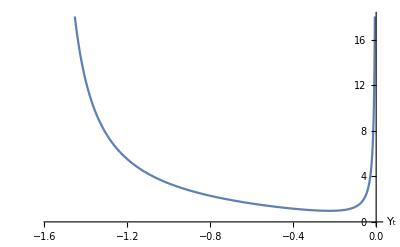

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_1.pdf

```mathematica
p = 0; a = 0.1; dp = 1; T = 1; dT = 0;
drift1 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_1.pdf",drift1]
```

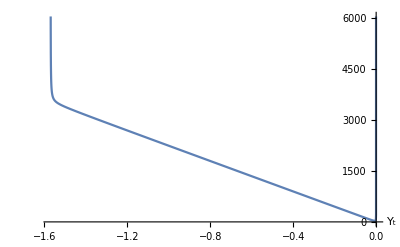

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_2.pdf

```mathematica
p = 0; a = 0.1; dp = 1; T = 1; dT = 1000;
drift2 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_2.pdf",drift2]
```

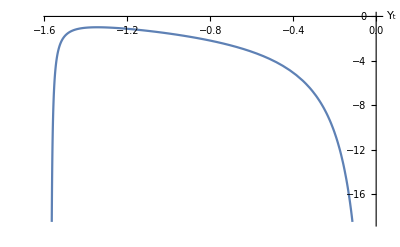

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_3.pdf

```mathematica
p = 1; a = 0.1; dp = -1; T = 1; dT = 0;
drift3 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_3.pdf",drift3]
```

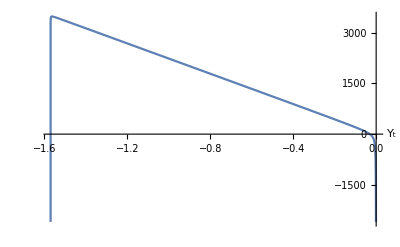

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_4.pdf

```mathematica
p = 1; a = 0.1; dp = -1; T = 1; dT = 1000;
drift4 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_4.pdf",drift4]
```

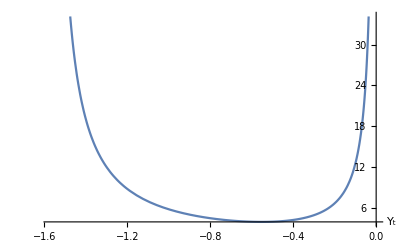

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_5.pdf

```mathematica
p = 1/2; a = 0.1; dp = 1; T = 1; dT = 0;
drift5 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_5.pdf",drift5]
```

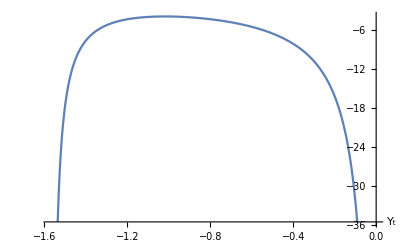

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_6.pdf

```mathematica
p = 1/2; a = 0.1; dp = -1; T = 1; dT = 0;
drift6 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_6.pdf",drift6]
```

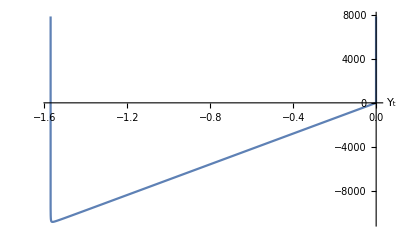

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_7.pdf

```mathematica
p = 0.01; a = 0.1; dp = 0.1; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift7 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_7.pdf",drift7]
```

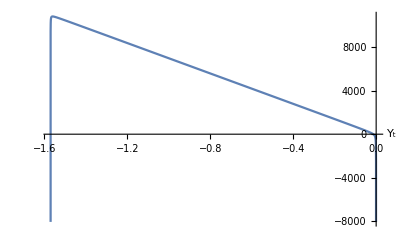

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_8.pdf

```mathematica
p = 0.01; a = 0.1; dp = -0.1; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift8 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_8.pdf",drift8]
```

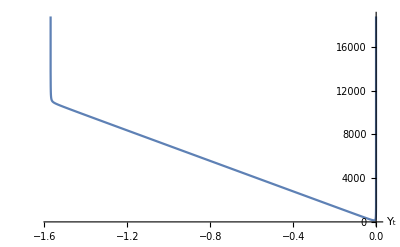

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_9.pdf

```mathematica
p = 0.99; a = 0.1; dp = 0.1; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(dp^2)/(p-1)^2;
drift9 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_9.pdf",drift9]
```

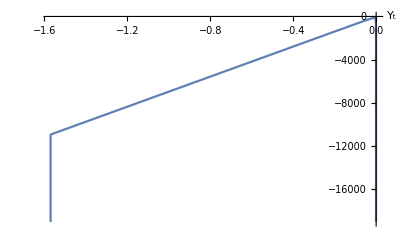

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_10.pdf

```mathematica
p = 0.99; a = 0.1; dp = -0.1; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(dp^2)/(p-1)^2;
drift10 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_10.pdf",drift10]
```

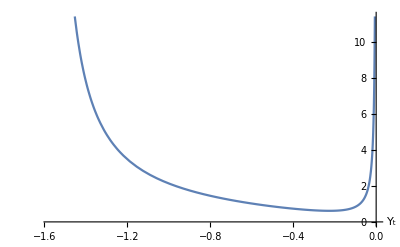

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_11.pdf

```mathematica
p = 0.5; a = 0.1; dp = 0.2; T = Abs[dp]/Max[p,1-p]; dT = 0;
drift11 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_11.pdf",drift11]
```

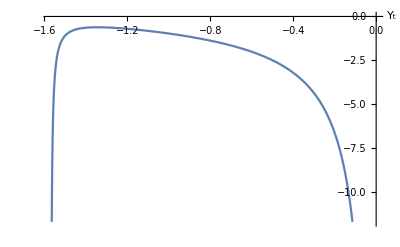

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_12.pdf

```mathematica
p = 0.5; a = 0.1; dp = -0.2; T = Abs[dp]/Max[p,1-p]; dT = 0;
drift12 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_12.pdf",drift12]
```

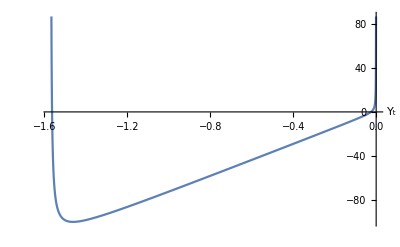

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_13.pdf

```mathematica
p = 0.1; a = 0.1; dp = 0.15; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift13 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_13.pdf",drift13]
```

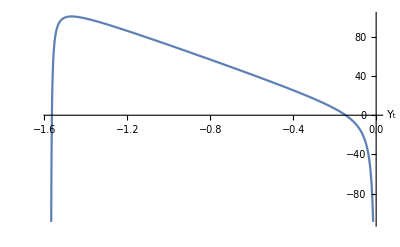

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_14.pdf

```mathematica
p = 0.1; a = 0.1; dp = -0.15; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift14 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_14.pdf",drift14]
```

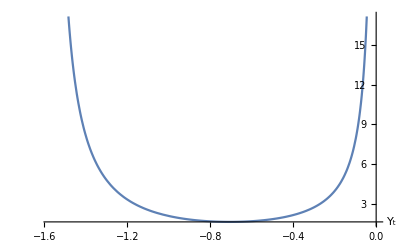

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_15.pdf

```mathematica
p = 0.9; a = 0.1; dp = 0.15; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift15 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_15.pdf",drift15]
```

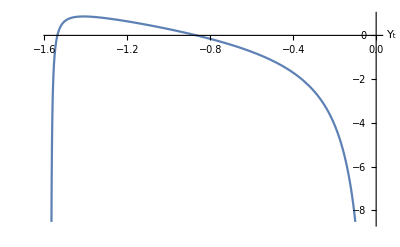

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_16.pdf

```mathematica
p = 0.9; a = 0.1; dp = -0.15; T = Abs[dp]/Max[p,1-p]; dT = Sign[dp]*(-dp^2)/p^2;
drift16 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_16.pdf",drift16]
```

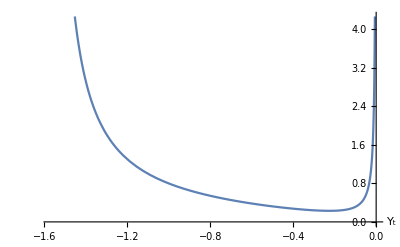

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_17.pdf

```mathematica
p = 0.1; a = 0.1; dp = 0.05; T = Abs[dp]/Max[p,1-p]; dT = 0;
drift17 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_17.pdf",drift17]
```

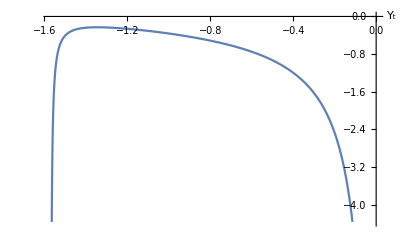

/home/caballrm/Dropbox/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/drift_z_18.pdf

```mathematica
p = 0.9; a = 0.1; dp = -0.05; T = Abs[dp]/Max[p,1-p]; dT = 0;
drift18 = Plot[fz[y],{y,-Pi/2,0},AxesLabel->{Subscript[Y,t]}]
Export[NotebookDirectory[]<>"drift_z_18.pdf",drift18]
```

# About Theta[t]: Notice that |p_dot|<=1/Delta_t=144.

```mathematica
Clear["Global`*"];
Theta[t_]=Max[T0,Abs[dp[t]]/Min[p[t],1-p[t]]]
ThetaT[t_]=D[Theta[t],t]
```

Max[T0,Abs[dp[t]]/Min[1-p[t],p[t]]]

Piecewise[{{0, (T0+Abs[dp[t]]/(-1+p[t])≥0&&p[t]≥1/2)||(p[t]<1/2&&T0-Abs[dp[t]]/p[t]≥0)}, {-(Abs'[dp[t]] dp'[t])/(-1+p[t])+(Abs[dp[t]] p'[t])/(-1+p[t])^2, T0+Abs[dp[t]]/(-1+p[t])<0&&p[t]≥1/2}, {(Abs'[dp[t]] dp'[t])/p[t]-(Abs[dp[t]] p'[t])/p[t]^2, True}}]

```mathematica
FullSimplify[%59]
```

Piecewise[{{(p[t] Abs'[dp[t]] dp'[t]-Abs[dp[t]] p'[t])/p[t]^2, T0<Abs[dp[t]]/p[t]&&2 p[t]<1}, {(-(-1+p[t]) Abs'[dp[t]] dp'[t]+Abs[dp[t]] p'[t])/(-1+p[t])^2, T0+Abs[dp[t]]/(-1+p[t])<0&&2 p[t]≥1}, {0, True}}]